# Predicting Climate Risks

## MGT529- Data Science and Machine Learning II

Jeanne Fernandez, Dario Scalabrin

```mathematica
Import[ "https://lh6.googleusercontent.com/dup3mfyN4nWaN1JjE6MmzOEbbUNCz1CBLGP2BASwjEzTTwfwwn9vZz_Tdap3rQJIwYM=w2400"]
```

-Graphics-

## Data Loading & Cleaning

### Data Loading

```mathematica
(*Import dataset sample*)
ds = Import["https://raw.githubusercontent.com/scalabrindario/predicting-climate-risks/main/data/dataset.csv", "Dataset", "HeaderLines" -> 1];
(*Import company information*)
comp = Import["https://raw.githubusercontent.com/scalabrindario/predicting-climate-risks/main/data/company_information.csv", "Dataset", "HeaderLines" -> 1];
```

### Data Cleaning

```mathematica
(*Drop emtpy column*)
ds = KeyDrop[{""}]@ds; 
(*Rename columns*)
ds = ds[All,KeyMap[Replace[{"Ultimate Parent Name"->"Company", "Ultimate Parent ISIN"->"ISIN","ExposureScore_Composite_ModerateHigh_2020" -> "Risk2020",
"ExposureScore_Composite_ModerateHigh_2030" -> "Risk2030","ExposureScore_Composite_ModerateHigh_2040" -> "Risk2040","ExposureScore_Composite_ModerateHigh_2050" -> "Risk2050","ExposureScore_Composite_ModerateHigh_2060" ->"Risk2060",
"ExposureScore_Composite_ModerateHigh_2070" -> "Risk2070","ExposureScore_Composite_ModerateHigh_2080" -> "Risk2080",
"ExposureScore_Composite_ModerateHigh_2090"-> "Risk2090"}]]];
RandomSample[ds, 5]
(*Drop emtpy column*)
comp = KeyDrop[{""}]@comp; 
RandomSample[comp, 5]
```

## Feature Engineering

### Integral Score

Our goal it to give a summary of the risk approximation by decade into one scalar statistic, called Integral Score. 
We first visualise several options for this score, given the risk values by decade.
One can fit a function given the risk approximation for several years, and then integrate the resulting curve.
The choice of score then boils down to the choice of approximation.

{76,75,72,66,65,66,67,67}

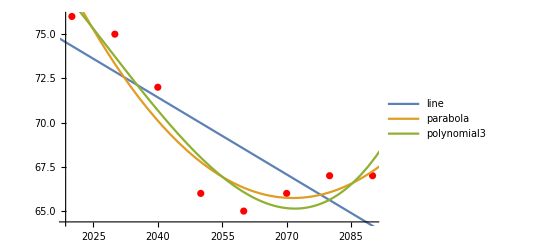

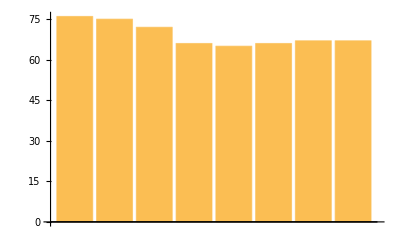

Linear approximation (line): 5481.9

Quardatic approximation (parabola): 5493.65

Third degree approximation (polynomial3): 5509.21

Rectangle approximation (barchart): 5540

```mathematica
(*Select timeframe*)
x = {2020, 2030, 2040,2050,2060,2070, 2080, 2090};
(*Pick one row at random for scores display*)
yRandom = Normal@Values@RandomSample[ds[All, {6;;13}],1][[1,1]] 
data = Transpose@Normal@{x,yRandom};
(*Different fit of parameterization functions*)
line = Fit[data, {1,z}, z];
parabola = Fit[data, {1,z,z^2}, z];
polynomial3 = Fit[data, {1,z,z^2,z^3}, z];
(*Display Risk values for selected timeframe, alongside with parameterization attempts*)
Show[ListPlot[data,PlotStyle->Red],Plot[{line, parabola, polynomial3},{z,2010,2100}, PlotLegends->"Expressions"]]
BarChart[yRandom]
Print["Linear approximation (line): ", Integrate[line,{z,2020,2100}]]
Print["Quardatic approximation (parabola): ",Integrate[parabola,{z,2020,2100}]]
Print["Third degree approximation (polynomial3): ",Integrate[polynomial3,{z,2020,2100}]]
Print["Rectangle approximation (barchart): ",(Total@yRandom)*10]
```

We note that all the approximations are in the same order of magnitude. For the sake of simplicity and to avoid overfitting, we choose the linear approximation. We add the chosen Integral Score to the dataset.

```mathematica
(*Update dataset with chosen intergral score*)
intColumn =ds[All,<|"integralScore"->Integrate[
Fit[Transpose@Normal@{x,{#Risk2020,#Risk2030,#Risk2040,#Risk2050,#Risk2060,#Risk2070,#Risk2080,#Risk2090}}, {1,z}, z]
,{z,2020,2100}]|>&];
newds=Join[ds,intColumn,2];
RandomSample[newds, 5]
```

### Computing Average of Integral Score

```mathematica
(*Group assets by companies and compute their mean integral score*) 
avgds= newds[GroupBy[{#Company}&]/*Values,<|"Company"->Query[First,"Company"],"ISIN"->Query[First,"ISIN"],"integralScore"->Query[Mean,"integralScore"]|>] ;
RandomSample[avgds, 5]
```

### Merge the two datasets

```mathematica
(*Merge two datasets (companies information and physical risk assets) and drop lines with no ISIN*)
merged = JoinAcross[avgds,comp,"ISIN"];
merged = merged[Select[#ISIN !=""&]];
RandomSample[merged,5]
```

### Create Ratings from Integral Score

```mathematica
(*Rescale integral score with min-max method*)
MinMaxScaler[value_]:=Rescale[value,{Min[merged[All, "integralScore"]],Max[merged[All, "integralScore"]]}];
MinMaxScaledList = Map[MinMaxScaler, merged[All, "integralScore"]];
(*Convert a numerical variable into categorical data*)
RatingCreator[value_]:= 
If[Between[value,{0,0.2}], "A", 
If[Between[value,{0.2,0.4}], "B", 
If[Between[value,{0.4,0.6}], "C",
If[Between[value,{0.6,0.8}], "D",
If[Between[value,{0.8,1}], "E",   
]]]]]; 
RatingsList = Map[RatingCreator, MinMaxScaledList];
 (*Convert the list into a dataset*)
IntScaledDat=Dataset[<|"IntScaled"->#|>&/@Normal[MinMaxScaledList]];
(*Convert the list into a dataset*)
RatingsDat=Dataset[<|"Ratings"->#|>&/@Normal[RatingsList]];
(*Add Scaled Integral column to the dataset*)
finalds = Join[merged,IntScaledDat,2]; 
(*Add Rating column to the dataset*)
finalds = Join[finalds,RatingsDat,2];
RandomSample[finalds, 5]
```

### Add to the dataset the Total Carbon Intensity

```mathematica
(*Keep only carbon intensity columns*)
CI1L = Normal[finalds[All, "Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"]];
CI2L = Normal[finalds[All,  "Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"]];
CI3L = Normal[finalds[All,  "Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"]];
(*Convert the list into a dataset*)
CItotDat=Dataset[<|"Carbon Intensity Total (tonnes CO2e/USD mn)"->#|>&/@Normal[Total[{CI1L, CI2L, CI3L}]]]; 
(*Add Carbon Intensity-Scope Total column to the dataset*)
finalds = Join[finalds,CItotDat,2]; 
RandomSample[finalds,5]
```

## Exploratory Data Analysis

### General Plots

```mathematica
(*Check dimensions of the dataset*)
Dimensions@finalds
```

{4787,17}

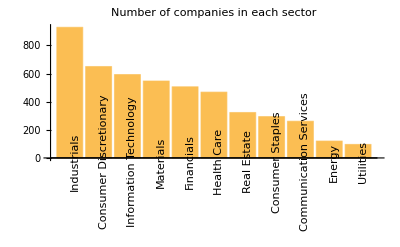

```mathematica
(*Show the number of companies in each sector*)
x1 = ReverseSort@Counts[finalds[All, "GICS Sector Name"]];
BarChart[x1,ChartLabels ->Placed[Normal@Keys@x1,Below, Rotate[#, Pi/2] &],PlotLabel->"Number of companies in each sector"]
```

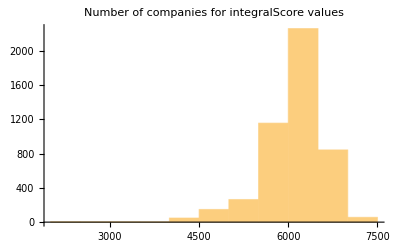

```mathematica
(*Distribution of companies with respect to integral score*)
Histogram[finalds[All, "integralScore"],PlotLabel->"Number of companies for integralScore values"]
```

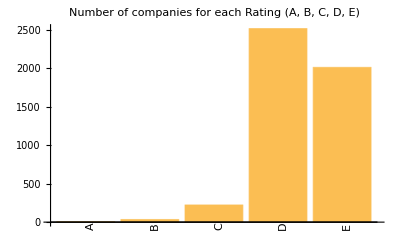

```mathematica
(*Distribution of predicted score across companies*)
x2 = Counts[finalds[All, "Ratings"]];
x3 = {x2["A"], x2["B"], x2["C"], x2["D"], x2["E"]};
BarChart[x3,ChartLabels ->Placed[{"A","B","C","D","E"},Below, Rotate[#, Pi/2] &],PlotLabel->"Number of companies for each Rating (A, B, C, D, E) "]
```

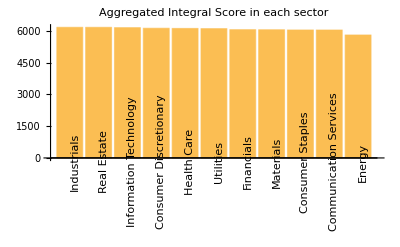

```mathematica
(*Average Integral score per sector*)
x4 = ReverseSort@finalds[GroupBy["GICS Sector Name"],Mean,{"integralScore"}];
x5 = Flatten@Values@Values@Normal@x4;
BarChart[x5,ChartLabels -> Placed[Normal@Keys@x4,Below, Rotate[#, Pi/2] &],PlotLabel->"Aggregated Integral Score in each sector"]
```

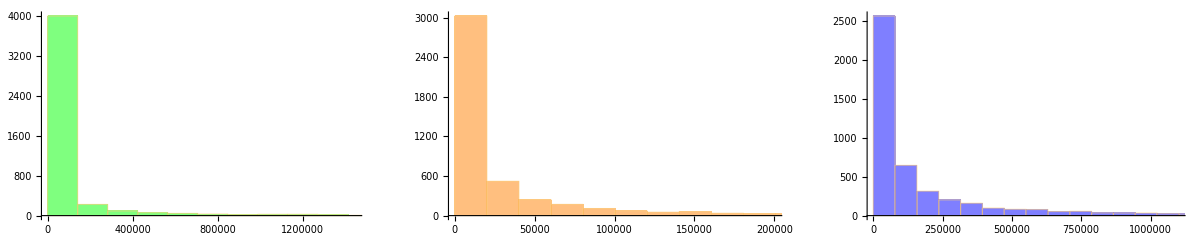

```mathematica
(*Carbon emission (Scope 1,2,3) distribution across dataset*)
g1=Histogram[finalds[All, "Carbon-Scope 1  (tonnes CO2e)"],ChartStyle->{Directive[Green,Opacity[.5]]}];
g2=Histogram[finalds[All, "Carbon-Scope 2  (tonnes CO2e)"],ChartStyle->{Directive[Orange,Opacity[.5]]}];
g3=Histogram[finalds[All, "Carbon-Scope 3 (tonnes CO2e)"],ChartStyle->{Directive[Blue,Opacity[.5]]}];
GraphicsRow[{g1,g2, g3},PlotLabel->"Carbon-Scope 1,2,3 (tonnes CO2e)"]
```

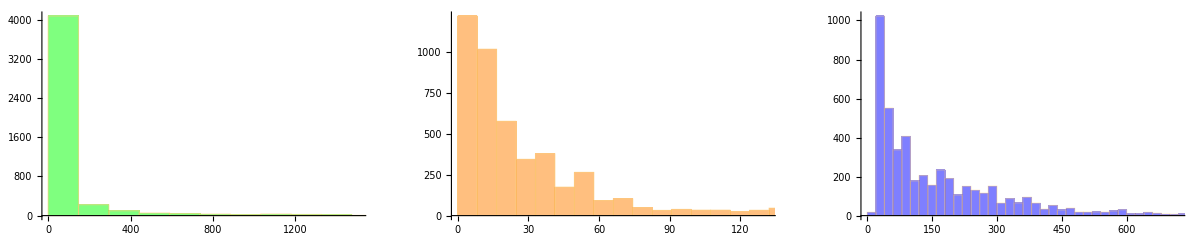

```mathematica
(*Carbon intensity (Scope 1,2,3) distribution across dataset*)
j1=Histogram[finalds[All, "Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Green,Opacity[.5]]}];
j2=Histogram[finalds[All, "Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Orange,Opacity[.5]]}];
j3=Histogram[finalds[All, "Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Blue,Opacity[.5]]}];
GraphicsRow[{j1,j2, j3},PlotLabel->"Carbon Intensity-Scope 1,2,3 (tonnes CO2e/USD mn)"]
```

### Cross-column Analysis

Now we try to visualise the eventual dependencies of the columns of the dataset. As we previously see, the distribution of carbon emissions and intensity are skewed, so we apply the natural logarithm before visualizing the data.

```mathematica
revLog = Normal@finalds[All,"Revenue (USD mn)" ][Log];
scope1Log =  Normal@finalds[All,"Carbon-Scope 1  (tonnes CO2e)" ][Log];
scope2Log =  Normal@finalds[All,"Carbon-Scope 2  (tonnes CO2e)" ][Log];
scope3Log =  Normal@finalds[All,"Carbon-Scope 3 (tonnes CO2e)" ][Log];
scopeTotLog =  Normal@finalds[All,"Carbon Intensity Total (tonnes CO2e/USD mn)"][Log];
dataRev  =Dataset[<|"Log of Revenues (USD mn)"->Normal@revLog |>]//Transpose;
dataScope1Log  =Dataset[<|"Log of Scope 1 emissons (tonnes CO2e)"->Normal@scope1Log |>]//Transpose;
dataScope2Log  =Dataset[<|"Log of Scope 2 emissons (tonnes CO2e)"->Normal@scope2Log |>]//Transpose;
dataScope3Log  =Dataset[<|"Log of Scope 3 emissons (tonnes CO2e)"->Normal@scope3Log |>]//Transpose;
dataScopeTotLog  =Dataset[<|"Log of Carbon Intensity Total (tonnes CO2e/USD mn)"->Normal@scopeTotLog |>]//Transpose;
finalds2 = Join[finalds,dataRev ,2];
finalds3 = Join[finalds2,dataScope1Log ,2];
finalds4 = Join[finalds3,dataScope2Log ,2];
finalds5 = Join[finalds4,dataScope3Log ,2];
finalds6 = Join[finalds5,dataScopeTotLog ,2];
```

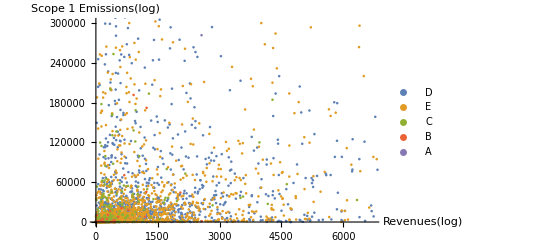

```mathematica
(*Visualisation before applying Log*)
ListPlot[finalds3[GroupBy[Key["Ratings"]],All,{"Revenue (USD mn)","Carbon-Scope 1  (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 1 Emissions(log)"}]
```

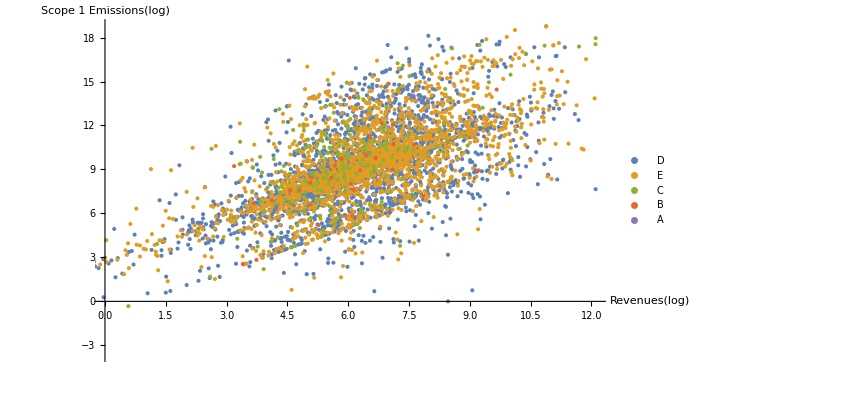

```mathematica
(*Visualisation of revenues VS scope 1 emissions after applying Log with corresponding rating*)
ListPlot[finalds3[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Scope 1 emissons (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 1 Emissions(log)"}]
```

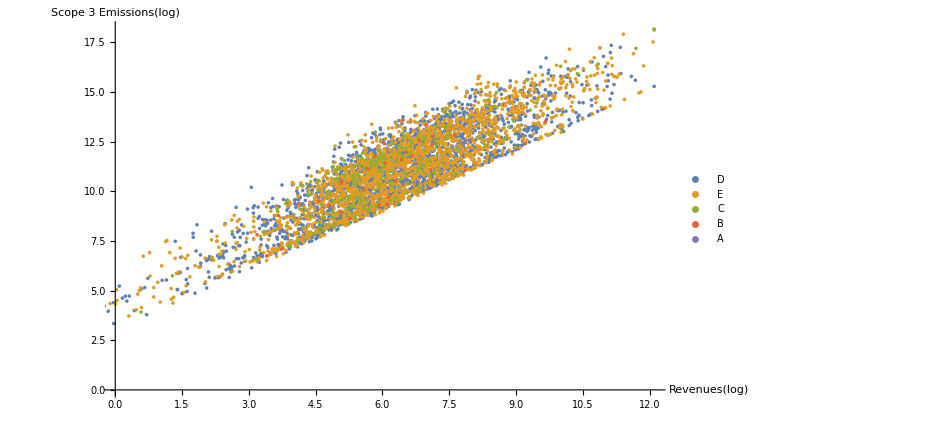

```mathematica
(*Visualisation of revenues VS scope 3 emissions after applying Log with corresponding rating*)
ListPlot[finalds5[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Scope 3 emissons (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 3 Emissions(log)"}]
```

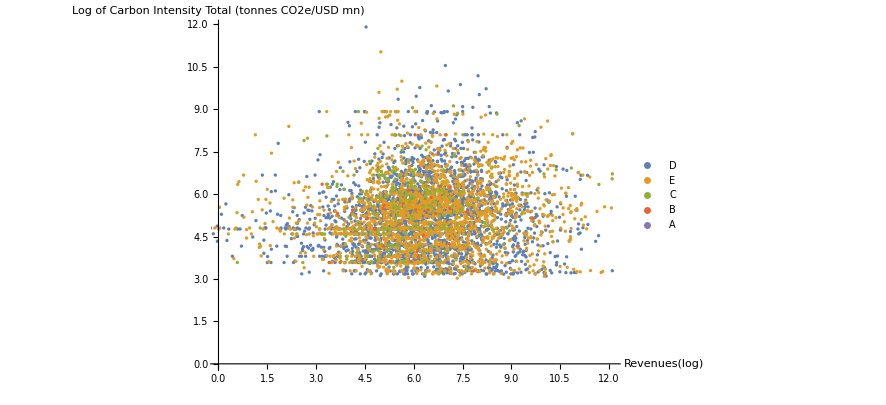

```mathematica
(*Visualisation of revenues VS total carbon intensity after applying Log with corresponding rating*)
ListPlot[finalds6[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Carbon Intensity Total (tonnes CO2e/USD mn)"}], AxesLabel->{"Revenues(log)","Log of Carbon Intensity Total (tonnes CO2e/USD mn)"}]
```

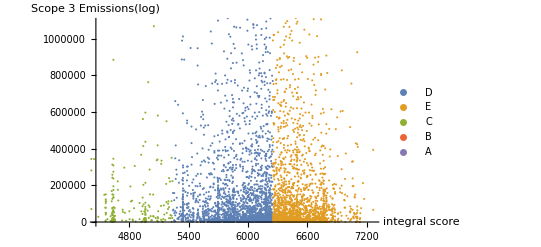

```mathematica
(*Visualisation of integral score VS scope 3 emissions after applying Log with corresponding rating*)
ListPlot[finalds5[GroupBy[Key["Ratings"]],All,{ "integralScore", "Carbon-Scope 3 (tonnes CO2e)"}], AxesLabel->{"integral score","Scope 3 Emissions(log)"}]
```

## Machine Learning

### Dataset Preparation

Prepare the dataset to use as an input for the machine learning models that we are going to create. In particular, we are going to divide the dataset in two new dataset: Training set, which includes 80% of all the rows of the dataset, while the Test set, which includes the remaining 20%.
The training set will be used to train our models, while the test set in order to understand the accuracy of our models.

```mathematica
(*Drop columns that are not needed for machine learning techniques*)
datasetML = KeyDrop[{"Company", "ISIN", "TCUID", "integralScore", "IntScaled","Carbon-Scope 1  (tonnes CO2e)", "Carbon-Scope 2  (tonnes CO2e)", "Carbon-Scope 3 (tonnes CO2e)", "Carbon Intensity Total (tonnes CO2e/USD mn)"}]@finalds; 
(*Retrieve the number of rows and columns of the dataset*)
{nobs,ncol}=Dimensions[datasetML];
{trainingset,testset}=TakeDrop[RandomSample[datasetML],Round[nobs*0.8,1]];(*Divide the dataset in training set and test set*)
(*Create an empty association, to fill in with accuracy of our models*)AccuracyAss = Association[];
```

### Classification

#### Logistic Regression

```mathematica
(*Train a classifier using Logistic Regression method*)
cRisk = Classify[trainingset->"Ratings",Method->"LogisticRegression"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 7)
Classes | ,,ABCDE
Accuracy | (62.42.5) %
Method | LogisticRegression
Single evaluation time | 7.24 ms/example
Batch evaluation speed | 6.75 examples/ms
Loss | 0.758 ± 0.029
Model memory | 438. kB
Training examples used | 3830 examples
Training time | 9.25 s
 |

The accuracy is: 0.599791

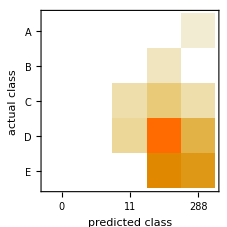

```mathematica
(*Test the classifier on the test set*)
cm =ClassifierMeasurements[cRisk,testset]; 
(*Plot the accuracy of our model*)
Print["The accuracy is: ",cm["Accuracy"] ]
AccuracyAss = Append[AccuracyAss, "LogisticRegression"->cm["Accuracy"]];
(*Plot the Confusion Matrix*)
cm["ConfusionMatrixPlot"]
```

#### RandomForest

```mathematica
(*Train a classifier using Breiman–Cutler ensembles of decision trees*)
cRisk = Classify[trainingset->"Ratings",Method->"RandomForest"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 7)
Classes | ,,ABCDE
Accuracy | (57.32.1) %
Method | RandomForest
Single evaluation time | 3.05 ms/example
Batch evaluation speed | 29.4 examples/ms
Loss | 1.12 ± 0.0095
Model memory | 976. kB
Training examples used | 5261 examples
Training time | 4.77 s
 |

```mathematica
(*Test our classifier on the test set*)
cm =ClassifierMeasurements[cRisk,testset]; 
(*Plot the accuracy of our model*)
Print["The accuracy is: ",cm["Accuracy"] ]
AccuracyAss = Append[AccuracyAss, "RandomForest"->cm["Accuracy"]];
(*Plot the Confusion Matrix*)
cm["ConfusionMatrixPlot"]
```

The accuracy is: 0.599791

-Graphics-

#### SupportVectorMachine

```mathematica
(*Train a classifier using a support vector machine*)
cRisk = Classify[trainingset->"Ratings",Method->"SupportVectorMachine"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 7)
Classes | ,,ABCDE
Accuracy | (53.81.3) %
Method | SupportVectorMachine
Single evaluation time | 22.6 ms/example
Batch evaluation speed | 1.22 examples/ms
Loss | 1.01 ± 0.033
Model memory | 3.3 MB
Training examples used | 3830 examples
Training time | 50.5 s
 |

The accuracy is: 0.568443

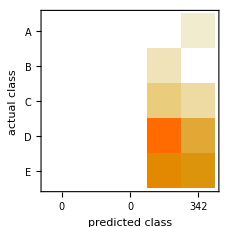

```mathematica
(*Test our classifier on the test set*)
cm =ClassifierMeasurements[cRisk,testset]; 
(*Plot the accuracy of our model*)
Print["The accuracy is: ",cm["Accuracy"] ]
AccuracyAss = Append[AccuracyAss, "SupportVectorMachine"->cm["Accuracy"]];
(*Plot the Confusion Matrix*)
cm["ConfusionMatrixPlot"]
```

#### Nearest Neighbors

```mathematica
(*Train a classifier using nearest neighbor*)
cRisk = Classify[trainingset->"Ratings",Method->"NearestNeighbors"]
Information[cRisk]
```

ClassifierFunction[…]

```mathematica
{{"Classifier information"}, {{{Data type, Mixed" (number: "7")"}, {Classes, ,","ABCDE}, {Accuracy, Quantity[(54.62.5), "Percent"]}, {Method, NearestNeighbors}, {Single evaluation time, Quantity[1.91, ("Milliseconds")/("Examples")]}, {Batch evaluation speed, Quantity[39.5, ("Examples")/("Milliseconds")]}, {Loss, 0.8072386138416003387`3." ± "0.0202444175573420829`2.}, {Model memory, Quantity[854., "Kilobytes"]}, {Training examples used, Quantity[5261, "Examples"]}, {Training time, Quantity[600., "Milliseconds"]}, {, }}}}
```

Classifier information
Data type | Mixed (number: 7)
Classes | ,,ABCDE
Accuracy | (54.62.5) %
Method | NearestNeighbors
Single evaluation time | 5.82 ms/example
Batch evaluation speed | 9.34 examples/ms
Loss | 0.807 ± 0.02
Model memory | 836. kB
Training examples used | 5261 examples
Training time | 600. ms
 |

```mathematica
(*Test our classifier on the test set*)
cm =ClassifierMeasurements[cRisk,testset]; 
Print["The accuracy is: ",cm["Accuracy"] ]
(*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "NearestNeighbors"->cm["Accuracy"]];
(*Plot the Confusion Matrix*)
cm["ConfusionMatrixPlot"]
```

The accuracy is: 0.568443

-Graphics-

### Neural Network

#### Encoding Data

Categorical variables cannot be used directly in neural networks and must be encoded as arrays.
Therefore, we create “Class” encoders that encode the categorical variables as one-hot encoded vectors

```mathematica
sectorEncoder=NetEncoder[{"Class",DeleteDuplicates[Normal[datasetML[All,"GICS Sector Name"]]],"UnitVector"}]
disclosureEncoder=NetEncoder[{"Class",DeleteDuplicates[Normal[datasetML[All, "Carbon Disclosure"]]],"UnitVector"}]
countryEncoder=NetEncoder[{"Class",DeleteDuplicates[Normal[datasetML[All, "Country"]]],"UnitVector"}]
```

NetEncoder[<>]

NetEncoder[<>]

NetEncoder[<>]

Applying the encoders to class labels produces unit vectors

```mathematica
sectorEncoder/@DeleteDuplicates[Normal[trainingset[All,"GICS Sector Name"]]];
disclosureEncoder/@DeleteDuplicates[Normal[trainingset[All,"Carbon Disclosure"]]];
countryEncoder/@DeleteDuplicates[Normal[trainingset[All,"Country"]]];
```

Applying the Decoder to class labels that we want to predict

```mathematica
ratingsDecoder = NetDecoder[{"Class",DeleteDuplicates[Normal[datasetML[All, "Ratings"]]] }];
```

#### Create a Neural Network

Create a neural network with an input corresponding to each feature and using a “Categorize” decoder to interpret the output of the net
The input features are first concatenated together before being further processed using one linear layer and a logistic sigmoid.

```mathematica
net=NetGraph[{CatenateLayer[],LinearLayer[],LogisticSigmoid},
{{NetPort["GICS Sector Name"],NetPort["Country"],NetPort["Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"],NetPort["Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"],NetPort["Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"],NetPort["Carbon Disclosure"],NetPort["Revenue (USD mn)"]}->1,1->2->3->NetPort["Ratings"]},
"GICS Sector Name"->sectorEncoder,"Country"->countryEncoder,"Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"->"Scalar","Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"->"Scalar","Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"->"Scalar","Carbon Disclosure"->disclosureEncoder,"Revenue (USD mn)"->"Scalar","Ratings"->ratingsDecoder]
```

NetGraph[<>]

#### Training the Net

Train the net on the training data. NetTrain will automatically attach a Cross Entropy Loss layer to the output of the net
We set up two parameters:
- “Max Training Rounds”: is an option that specifies how many times to traverse the training data
- “Learning Rate”: is an option that specifies the rate at which to adjust neural net weights in order to minimize the training loss.

```mathematica
results=NetTrain[net,trainingset,All,MaxTrainingRounds->1000, LearningRate->0.01];
netTrained=results["TrainedNet"]
```

NetGraph[<>]

#### Testing the Trained Neural Network

Plot the accuracy of the Neural Network on the Test Set

```mathematica
Print["The accuracy is: ",NetMeasurements[netTrained,testset,"Accuracy"]]
AccuracyAss = Append[AccuracyAss, "NeuralNetwork"->NetMeasurements[netTrained,testset,"Accuracy"]];
```

The accuracy is: 0.825078

### Comparing Accuracies

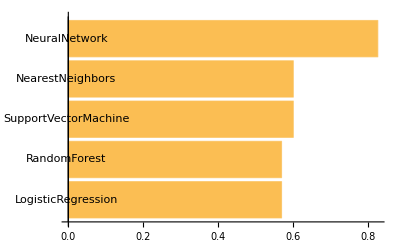

```mathematica
(*Plot the accuracy for each method tested previously*)
BarChart[Sort[AccuracyAss], ChartLabels->Keys[AccuracyAss], BarOrigin->Left]
```

```mathematica
AccuracyAss
```

<|LogisticRegression→0.599791,RandomForest→0.599791,SupportVectorMachine→0.568443,NearestNeighbors→0.568443,NeuralNetwork→0.825078|>

## Creating the API

We create an API for predicting climate risks using the previously defined Neural Network,  for any dataset respecting the same format.

### Defining the API

```mathematica
(*API definition*)
apiFunc = APIFunction[{
"Sector" -> "String" -> "Financials",
"Country" -> "String" -> "ITALY",
 "CarbInt1" -> "Number" -> 10000,
"CarbInt2" -> "Number" -> 10000,
"CarbInt3" -> "Number" -> 10000,
"CarbDisc" -> "String" -> "Value derived from data provided in Environmental/CSR",
"Revenues" -> "Number" -> 10000
},
netTrained[{#Sector,#Country, #CarbInt1, #CarbInt2,  #CarbInt3, #CarbDisc,  #Revenues}]&
];
```

### Deploying the API

```mathematica
(*Deploy API publicly on the cloud*)
apiFuncDeployed = CloudDeploy[
apiFunc,
"WebServices/APIRiskRating",
Permissions -> "Public"]
```

CloudObject::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

$Failed